```mathematica
∫_xt^1 ⅇ^((t-a) z) z^(n-2)ⅆz
```

```mathematica
∫_0^1 ⅇ^(-a z)z^(n-3)ⅆz
```

ConditionalExpression[a^(2-n) (Gamma[-2+n]-Gamma[-2+n,a]),Re[n]>2]

```mathematica
(∫_0^1 z ⅇ^(-a z) z^(n-3)ⅆz)/(a^(2-n) (Gamma[-2+n]-Gamma[-2+n,a]))
```

ConditionalExpression[(Gamma[-1+n]-Gamma[-1+n,a])/(a (Gamma[-2+n]-Gamma[-2+n,a])),Re[n]>1]

```mathematica
(Gamma[n-1]-Gamma[n-1,a])/(a (Gamma[-2+n]-Gamma[-2+n,a]))/.{n->7.5,a->8.5}//N
```

0.580746

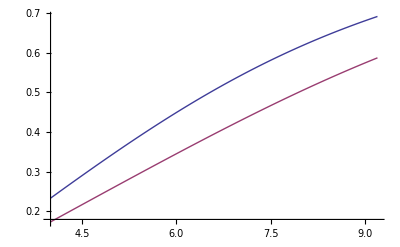

```mathematica
Plot[{(Gamma[n-1]-Gamma[n-1,a])/(a (Gamma[n-2]-Gamma[n-2,a]))/.a->8.5,(Gamma[n-1]-Gamma[n-1,a])/(a (Gamma[n-2]-Gamma[n-2,a]))/.a->11.5},{n,4,9.2}]
```

```mathematica
Gamma[5.5, .5]
```

52.3401

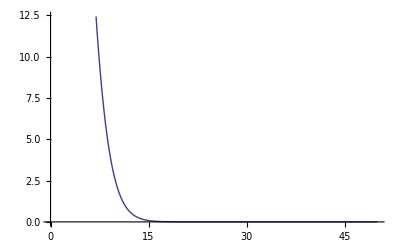

```mathematica
Plot[Gamma[5.5, x],{x,0.0, 50} ]
```

```mathematica
N[π,10]
```

3.141592654